# Chess tactics for beginners

Progetto di Matematica computazionale per l’anno accademico 2022/2023.
Collaborators: Andrea Accornero, Andrea Bianchi, Mattia Frega, Gabriele Magazzù.

```mathematica
cb[n_] := MatrixPlot[
  SparseArray[{i_, j_} :> Mod[1 + i + j, 2], {n, n}],
  ColorFunction -> GrayLevel, 
  FrameTicks -> {
    {#, #} &@ Table[{i, n - i + 1}, {i, n}],
    {#, #} &@ Table[{i, FromCharacterCode[ToCharacterCode["a"] + i - 1]}, {i, n}]},
  FrameStyle -> Bold
  ]

cb[8]
```

-Graphics-

permette di esportare lo stato delle scacchiera come file immagine, utile per comodità dell’utente ma anche per scrivere la nostra documentazione!

```mathematica
boardstatus := cb[12]
Export["boardstatus.gif",boardstatus]
ExpandFileName["boardstatus.gif"]
```

boardstatus.gif

C:\Users\matti\Documents\boardstatus.gif

ImportString è la funzione nativa per costruire la scacchiera

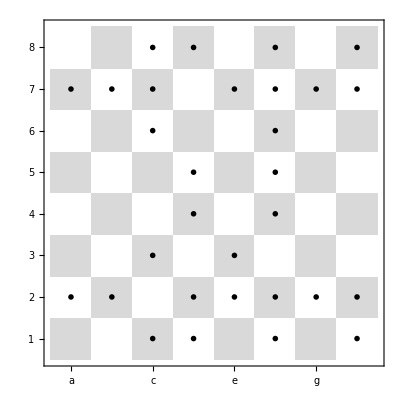

```mathematica
ImportString["2kr1b1r/ppp1qppp/2n2n2/3p1b2/3P1N2/2P1B3/PP1NQPPP/2KR1B1R b - - 3 11","FEN"]
```

Anche curiosamente personalizzabile

```mathematica
wKing = FindFaces[Entity["Person", "StephenWolfram::j276d"]["Image"], 
    "Image"] // First;
bKing = FindFaces[Entity["Person", "GuidoVanRossum::f5pfb"]["Image"], 
    "Image"] // First;
icons = <|"K" -> wKing, "P" -> -Graphics-, 
   "k" -> bKing, "p" -> -Graphics-|>;
```

```mathematica
ImportString["8/5k2/3p4/1p1Pp2p/pP2Pp1P/P4P1K/8/8 b - - 99 50",{"FEN","PositionRendering"},"Icons"->icons]//First
```

-Graphics-